Homework 1

## Problem 1.1

Greek letters can either be spelled out (as any other variable name) or the Greek letters can be formed by typing <esc>alpha<esc> to get α, for example. Since alpha and α are not taken to be the same thing, our convention will be to spell out the letters.

A block of mass m slides down an inclined plane that makes an angle theta with respect to the horizontal. The coefficient of kinetic friction is mu . What is the acceleration of the block? Use coordinates where x increases as you go down the plane.

•Use Newton's Second Law to find equations of motion for the x and y directions. 
Fx is the x component of the force, etc.
n is the normal force.
g is the acceleration of gravity.

```mathematica
Clear["`*"]
```

```mathematica
Fg = m * g
n=Cos[theta]*Fg
Ff = n * mu
Fx=Fg * Sin[theta] - Ff
Fy=0
```

g m

g m Cos[theta]

g m mu Cos[theta]

-g m mu Cos[theta]+g m Sin[theta]

0

### Need a hint?

Draw a free body diagram for the system. 
To see if you have sines and cosines right, think of the limiting case of =0. 
Since the motion is in the +x direction, the frictional force is in the -x direction.

### Solutions

These lines contain solutions to the question above.  If you execute this section  you will get feedback on these answers. Try not to look at the answers unless you get desperate.
Use the following instuction when you want to do this:
 •open the Edit tab
 •select Preferences
 •click to activate the Show Open/Close Icon for Cell Groups box
 •click on the small triangle that appeared on this worksheet

The names of any quantities I define end in a $ sign, so avoid using $ signs if you create any variable names.

```mathematica
n$=m*g*Cos[theta];
Fx$=m*g*Sin[theta]-mu*n;
Fy$=0;
If [FullSimplify[Solve[n$==n,m]]=={{}},Print["N is correct"],Print["N is incorrect"]]
If [FullSimplify[Solve[Fx$==Fx,m]]=={{}},Print["Fx is correct"],Print["Fx is incorrect"]]
If [FullSimplify[Solve[Fy$==Fy,m]]=={{}},Print["Fy is correct"],Print["Fy is incorrect"]]
n2$=m*g*Sin[theta];
If[FullSimplify[Solve[n2$==n,m]]=={{}},Print["Check your sines and cosines."]];
Fx2$=m*g*Cos[theta];
If[FullSimplify[Solve[Fx2$==Fx,m]]=={{}},Print["Check your sines and cosines."]];
Fx3$=m*g*Sin[theta];
If[FullSimplify[Solve[Fx3$==Fx,m]]=={{}},Print["Did you forget the frictional term?"]];
Fx4$=m*g*Cos[theta];
If[FullSimplify[Solve[Fx4$==Fx,m]]=={{}},Print["Check your sines and cosine and your frictional term."]];
Fx5$=m*g*Sin[theta]+mu*n;
If[FullSimplify[Solve[Fx5$==Fx,m]]=={{}},Print["The frictional force is in the -x direction."]];
```

N is correct

Fx is correct

Fy is correct

•Combine these equations to find the acceleration.
You can solve the equations by hand, but you can also use Mathematica to solve them for you.
Since this is partly Mathematica practice, we'll let Mathematica do it.
Let ax be the x component of a.

```mathematica
Clear[ax];  (*This helps if you have to re-execute this section.*)
eq1=Fx == m*ax
ax=ax/.Solve[eq1,ax][[1]]
```

-g m mu Cos[theta]+g m Sin[theta]==ax m

-g mu Cos[theta]+g Sin[theta]

### Solution

```mathematica
ax$=g*Sin[theta]-mu*g*Cos[theta];
If[FullSimplify[Solve[ax$==ax,g]]=={{}},Print["ax is correct"],Print["ax is incorrect"]]
```

ax is correct

•Let m=1 kg, =30 degrees, and =0.12. If x(0)=v(0)=0, find x(t) and v(t). Plot these functions over the time interval 0 to 1 sec.
Remember that angles must be in radians and π must be written as Pi.
We also need to define g.

```mathematica
m=1;
theta=30*Pi/180;
mu=.12;
g=9.8;
```

Note the syntax of the following equation:

```mathematica
Clear[x];
sol=DSolve[{x''[t]==ax,x[0]==0,x'[0]==0},x[t],t];
x=x[t]/.sol[[1]]
```

1.94078 t^2

The previous line defines x(t) as the solution of the differential equation. It allows us to plot it, differentiate it, etc.

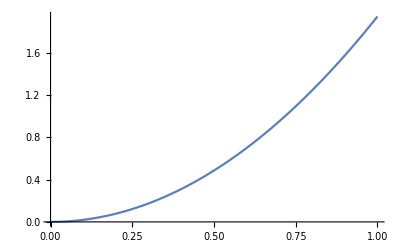

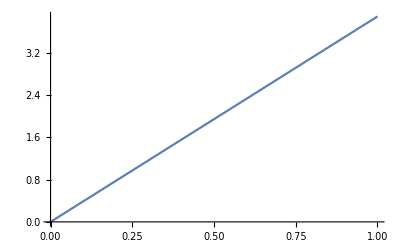

```mathematica
Plot[x,{t,0,1}]
y=D[x,t];
Plot[y,{t,0,1}]
```

## Problem 1.2

A sphere of mass m and radius R rolls without slipping down an inclined plane that makes an angle theta  with respect to the horizontal. The sphere has uniform mass density. What is the acceleration of the sphere? Use coordinates where x increases as you go down the plane. Look up the moment of inertia for a sphere if you need to.

```mathematica
Clear["`*"]
```

•Is there a frictional force? How do you know?
>> Type your anwer here: There is, because the sphere rolls down without slipping. The frictional force is what causes the sphere to rotate.

•Is there any energy loss to frictional forces? Why?
>> There is no energy loss because the frictional force vector is always orthogonal to the directional vector of motion (the direction of motion of the point that is in contact with the ground).

•Use Newton's Second Law to find equations of motion for the x and y directions.
Just call the frictional force Ff  for now.

```mathematica
Clear[Ff]
Fg = m* g
n=Fg * Cos[theta]
Fx=Fg * Sin[theta] - Ff
Fy=0
```

g m

g m Cos[theta]

-Ff+g m Sin[theta]

0

### Hint

Work the problem exactly as did Problem 1.1. We will use torque and the condition for rolling without slipping to deduce the frictional force.

### Solutions

```mathematica
n$=m*g*Cos[theta];
Fx$=m*g*Sin[theta]-Ff;
Fy$=0;
If[FullSimplify[Solve[n$==n,m]]=={{}},Print["n is correct"],Print["n is incorret"]];
If[FullSimplify[Solve[Fx$==Fx,m]]=={{}},Print["Fx is correct"],Print["Fx is incorrect"]];
If[FullSimplify[Solve[Fy$==F+a$,a$]]=={{a$->-F}},Print["Fy is correct"],Print["Fy is incorrect"]];
n2$=m*g*Sin[theta];
If[FullSimplify[Solve[n2$==n,m]]=={{}},Print["Check your sines and cosines."]];
Fx2$=m*g*Cos[θ]-Ff;
If[FullSimplify[Solve[Fx2$==Fx,m]]=={{}},Print["Check your sines and cosines."]];
Fx3$=m*g*Sin[theta];
If[FullSimplify[Solve[Fx3$==Fx,m]]=={{}},Print["Did you forget the frictional term?"]];
Fx4$=m*g*Cos[theta];
If[FullSimplify[Solve[Fx4$==Fx,m]]=={{}},Print["Check your sines and cosines and frictional term."]];
Fx5$=m*g*Sin[theta]-mu*n;
If[FullSimplify[Solve[Fx5$==Fx,m]]=={{}},Print["The frictional term does not equal mu*n for rolling friction.  Just us Ff"]];
Fx6$=m*g*Sin[theta];
If[FullSimplify[Solve[Fx6$==Fx,m]]=={{}},Print["The frictional force is in the -x direction"]];
```

n is correct

Fx is correct

Fy is correct

•Use the torque equation to find the frictional force in terms of acceleration.
Write I.  Mathematica reserves I for sqrt(-1), so we write MI for moment of inertia.
Let tau be torque.
The blank lines are an indication that you might need a few steps here - either on paper or in Mathematica.
You should always feel free to add lines as you need.

```mathematica
MI=2*m*R^2/5
alpha = ax / R
tau = MI * alpha == Ff * R
Ff=Ff/.Solve[tau, Ff][[1]]
```

(2 m R^2)/5

ax/R

(2 ax m R)/5==Ff R

(2 ax m)/5

### Hint

We know the torque is I*alpha on one hand and Ff*R on the other. Then we need to know how alpha relates to ax.

### Solution

```mathematica
Ff$=2*m*ax/5;
If[FullSimplify[Solve[Ff$==Ff,m]]=={{}},Print["Ff is correct"],Print["Ff is incorrect"]]
```

Ff is correct

#### Equations to solve for Ff - use only in case of emerency!

```mathematica
Clear[Ff]
alpha=ax/R
Ff=Ff/.Solve[MI*alpha==Ff*R,Ff][[1]]
```

•Combine these equations to find the overall acceleration.

```mathematica
Clear[ax];
eq2=Fx==m*ax
ax=ax/.Solve[eq2,ax][[1]]
```

-(2 ax m)/5+g m Sin[theta]==ax m

5/7 g Sin[theta]

### Solution

You may need to go back and re-assign ax if you have either cleared it or quit the kernel it was assigned in.

```mathematica
ax$=5/7*g*Sin[theta];
If[FullSimplify[Solve[ax$==ax,m]]=={{}},Print["ax is correct."],Print["ax is incorrect."]]
```

ax is correct.

## Paper Problems

-Graphics-

-Graphics-

-Graphics-